```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={θ<π/2, θ>-π/2,d>0,ϵ>0};
```

df[ζ_]=k(ζ- ⅈ d)^(θ/π)ζ^(-2 θ/π)(ζ+ ⅈ d)^(θ/π);
f[ζ_]=∫df[ζ]ⅆζ+c//Simplify;

```mathematica
f[ζ_]:=(k π)/(d^2(π-2 θ))  ζ^(1-(2 θ)/π) (ζ^2+ d^2)^(1+θ/π) Hypergeometric2F1[1,3/2,3/2-θ/π,-ζ^2/d^2]+c;
```

```mathematica
f[0]//Simplify
```

c

```mathematica
Limit[f[ϵ-ⅈ d],ϵ->0,Direction->-1]//Simplify
```

$Aborted

```mathematica
Limit[c+(k π (-ⅈ d)^(1-(2 θ)/π) (-2 ⅈ d ϵ)^(1+θ/π) Hypergeometric2F1[1,3/2,3/2-θ/π,-(-ⅈ d+ϵ)^2/d^2])/(d^2 (π-2 θ)),ϵ->0,Direction->-1]//Simplify
```

c-(2 ⅈ d ⅇ^(ⅈ θ) k √π θ Csc[θ] Gamma[3/2-θ/π])/((π-2 θ) Gamma[1-θ/π])

```mathematica
limgMinis=c-(2 ⅈ d ⅇ^(ⅈ θ) k √π θ Csc[θ] Gamma[3/2-θ/π])/((π-2 θ) Gamma[1-θ/π])
```

```mathematica
c=-d Tan[θ];
k  =-d(Gamma[-θ/π] Tan[θ])/Gamma[1/2-θ/π];
```

```mathematica
Block[{d=.6,θ =20*π/180},f[.000001-ⅈ d]]
```

0.0138614-0.638083 ⅈ

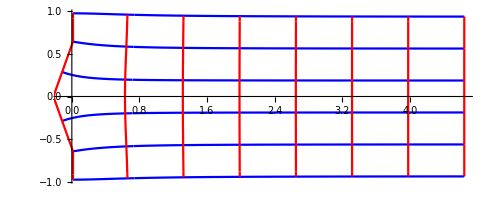

```mathematica
Block[{d=.6,θ =20*π/180,lim={.00001,5,-1,1}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]
```

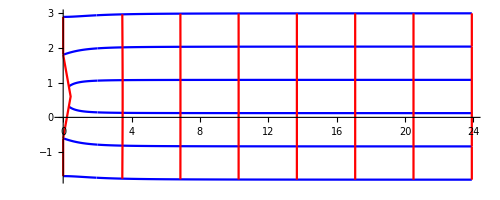

```mathematica
Block[{d=.6,θ =-20*π/180,lim={.00001,10,-1,1}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]
```

```mathematica
zz=Table[x+ⅈ y,{y,-1,1,.01},{x,0,5,0.1}];
```

```mathematica
Block[{d=.6,θ =20*π/180,lim={.00001,2,-1,1}},FF=f[zz]];
```

```mathematica
FF[[1,1]]
```

-0.436764-0.909446 ⅈ

```mathematica
Export["C:\\gits\\wave-current\\conformalMapping\\FF2.csv",FF]
```

C:\gits\wave-current\conformalMapping\FF2.csv

```mathematica
Export["C:\\gits\\wave-current\\conformalMapping\\FF_r.dat",Re@FF]
Export["C:\\gits\\wave-current\\conformalMapping\\FF_i.dat",Im@FF]
```

C:\gits\wave-current\conformalMapping\FF_r.dat

C:\gits\wave-current\conformalMapping\FF_i.dat

```mathematica
-(Gamma[-θ/π] Tan[θ])/(√π Gamma[1/2-θ/π])(ζ- ⅈ d)^(θ/π)ζ^(-2 θ/π)(ζ+ ⅈ d)^(θ/π)-df[ζ]//Simplify
```

0

```mathematica
f[0]//Simplify
```

-d Tan[θ]

```mathematica
Assuming[{θ<0,ϵ∈Reals},Limit[df[ϵ],ϵ->0,Direction->-1]]
```

0

```mathematica
Assuming[{θ>0,ϵ∈Reals},Limit[df[ϵ],ϵ->0,Direction->-1]]
```

-∞ Gamma[-θ/π]